```mathematica
Solve[{x==-x+x*y,y==-y/2-x*y-x^2},{x,y},Reals]
```

{{x→0,y→0}}

```mathematica
h[x_]:=a*x+b*x^2+c*x^3
```

```mathematica
fct = -h[x]/2-x*h[x]-x^2-h[-x+x*h[x]]
```

-x^2+1/2 (-a x-b x^2-c x^3)-x (a x+b x^2+c x^3)-a (-x+x (a x+b x^2+c x^3))-b (-x+x (a x+b x^2+c x^3))^2-c (-x+x (a x+b x^2+c x^3))^3

```mathematica
CoefficientList[fct,x]
```

{0,a/2,-1-a-a^2-(3 b)/2,-b+a b+c/2,-a^2 b+2 b^2-c-4 a c,-2 a b^2+3 a^2 c-b c,-b^3-a^3 c+4 a b c-3 c^2,-3 a^2 b c+b^2 c+6 a c^2,-3 a b^2 c-3 a^2 c^2+5 b c^2,-b^3 c-6 a b c^2+3 c^3,-3 b^2 c^2-3 a c^3,-3 b c^3,-c^4}

```mathematica
Solve[{a/2==0,-1-a-a^2-(3 b)/2==0,-b+a b+c/2==0},{a,b,c},Reals]
```

{{a→0,b→-2/3,c→-4/3}}

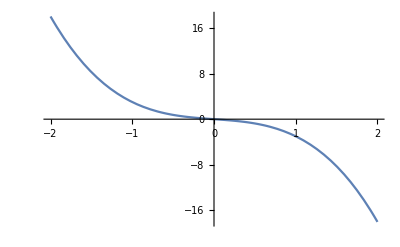

```mathematica
Plot[-x-2x^3/3-4x^3/3,{x,-2,2}]
```